# MS-C1650 - Numerical Analysis Week 16: Lecture 2: Solving Equations

## Harri Hakula, 2021

## Bisection Method

```mathematica
Clear@BisectionMethod
BisectionMethod::signs="`1` and `2` have same signs?";
BisectionMethod[fun_,{a0_?NumericQ,b0_?NumericQ},delta_?NumericQ]:=Block[{err,c,a=a0,b=b0,fa,fb,fc,conv={}},
err={};
fa=fun[a];
fb=fun[b];
While[Abs[b-a]>2delta,
AppendTo[err,Abs[b-a]];
c=Mean[{a,b}];
AppendTo[conv,c];
fc=fun[c];
If[Sign[fc]≠Sign[fb],
a=c;
fa=fc,
b=c;
fb=fc
]
];
{c,conv}
]/;Sign[fun[a0]]≠Sign[fun[b0]];
BisectionMethod[fun_,{a_?NumericQ,b_?NumericQ},delta_?NumericQ]:=Message[BisectionMethod::signs,fun[a],fun[b]]/;Sign[fun[a]]==Sign[fun[b]];
```

### Example: f(x) = (5-x)*Exp[x]-5

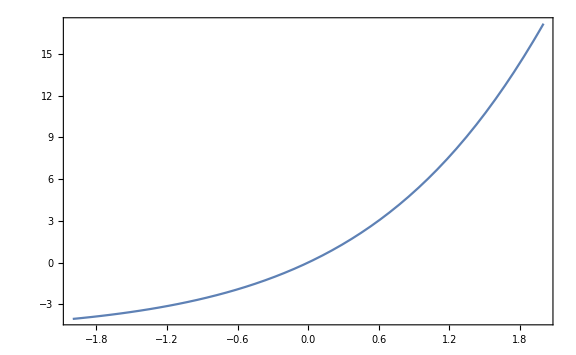

```mathematica
Plot[(5-x)*Exp[x]-5,{x,-2,2},Frame->True,ImageSize->Large]
```

```mathematica
{res,evx}=BisectionMethod[Function[x,(5-x)*Exp[x]-5],{-2.0,2.0},.01]
```

{0.015625,{0.,1.,0.5,0.25,0.125,0.0625,0.03125,0.015625}}

```mathematica
ek=Abs[Rest@evx]
data=Transpose[{Most[ek],Rest[ek]}]
```

{1.,0.5,0.25,0.125,0.0625,0.03125,0.015625}

{{1.,0.5},{0.5,0.25},{0.25,0.125},{0.125,0.0625},{0.0625,0.03125},{0.03125,0.015625}}

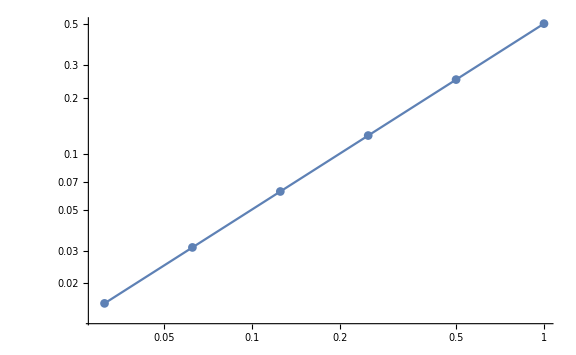

```mathematica
ListLogLogPlot[data,Joined->True,PlotMarkers->Automatic,ImageSize->Large]
```

```mathematica
Last@CoefficientList[Normal[LinearModelFit[Map[Log,data,{2}],{1,x},x]],x]
```

1.

## Bisection Method: f(x) = x^2-2

```mathematica
{res,evx}=BisectionMethod[Function[x,x^2-2],{0.0,2.0},.0000001]
```

{1.41421,{1.,1.5,1.25,1.375,1.4375,1.40625,1.42188,1.41406,1.41797,1.41602,1.41504,1.41455,1.41431,1.41418,1.41425,1.41422,1.4142,1.41421,1.41421,1.41421,1.41421,1.41421,1.41421,1.41421}}

```mathematica
ek=Abs[Sqrt[2]-evx]
data=Transpose[{Most[ek],Rest[ek]}]
```

{0.414214,0.0857864,0.164214,0.0392136,0.0232864,0.00796356,0.00766144,0.000151062,0.00375519,0.00180206,0.0008255,0.000337219,0.0000930783,0.0000289921,0.0000320431,1.52552×10^-6,0.0000137333,6.10388×10^-6,2.28918×10^-6,3.81831×10^-7,5.71843×10^-7,9.50061×10^-8,1.43413×10^-7,2.42032×10^-8}

{{0.414214,0.0857864},{0.0857864,0.164214},{0.164214,0.0392136},{0.0392136,0.0232864},{0.0232864,0.00796356},{0.00796356,0.00766144},{0.00766144,0.000151062},{0.000151062,0.00375519},{0.00375519,0.00180206},{0.00180206,0.0008255},{0.0008255,0.000337219},{0.000337219,0.0000930783},{0.0000930783,0.0000289921},{0.0000289921,0.0000320431},{0.0000320431,1.52552×10^-6},{1.52552×10^-6,0.0000137333},{0.0000137333,6.10388×10^-6},{6.10388×10^-6,2.28918×10^-6},{2.28918×10^-6,3.81831×10^-7},{3.81831×10^-7,5.71843×10^-7},{5.71843×10^-7,9.50061×10^-8},{9.50061×10^-8,1.43413×10^-7},{1.43413×10^-7,2.42032×10^-8}}

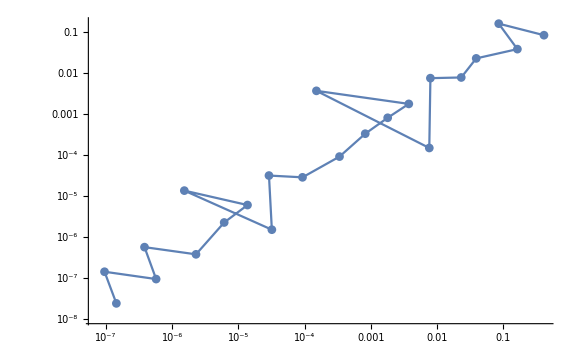

```mathematica
ListLogLogPlot[data,Joined->True,PlotMarkers->Automatic,ImageSize->Large]
```

```mathematica
Last@CoefficientList[Normal[LinearModelFit[Map[Log,data,{2}],{1,x},x]],x]
```

0.955658

## Newton’s Method

```mathematica
Example: f(x) = (5-x)*Exp[x]-5
```

```mathematica
fun=(5-x)Exp[x]-5
```

-5+ⅇ^x (5-x)

```mathematica
{res,{evx}}=Reap[FindRoot[fun==0,{x,3},EvaluationMonitor:>Sow[x]]]
```

{{x→-2.61713×10^-17},{{3.,1.24894,0.406711,0.0549145,0.00111209,4.63619×10^-7,8.0576×10^-14,-2.61713×10^-17}}}

```mathematica
ek=Abs[(x/.res)-evx]
```

{3.,1.24894,0.406711,0.0549145,0.00111209,4.63619×10^-7,8.06022×10^-14,0.}

```mathematica
data=Transpose[{Most[ek],Rest[ek]}]
```

{{3.,1.24894},{1.24894,0.406711},{0.406711,0.0549145},{0.0549145,0.00111209},{0.00111209,4.63619×10^-7},{4.63619×10^-7,8.06022×10^-14},{8.06022×10^-14,0.}}

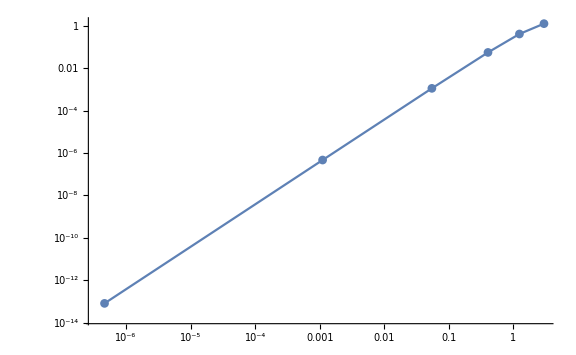

```mathematica
ListLogLogPlot[data,Joined->True,PlotMarkers->Automatic,ImageSize->Large]
```

```mathematica
Last@CoefficientList[Normal[LinearModelFit[Map[Log,Most@data,{2}],{1,x},x]],x]
```

1.96009

## Newton’s Method

```mathematica
Example: f(x) = x^2
```

```mathematica
fun=x^2
```

x^2

```mathematica
{res,{evx}}=Reap[FindRoot[fun==0,{x,3},EvaluationMonitor:>Sow[x]]]
```

{{x→5.58794×10^-9},{{3.,1.5,0.75,0.375,0.1875,0.09375,0.046875,0.0234375,0.0117188,0.00585938,0.00292969,0.00146484,0.000732422,0.000366211,0.000183105,0.0000915527,0.0000457764,0.0000228882,0.0000114441,5.72205×10^-6,2.86102×10^-6,1.43051×10^-6,7.15256×10^-7,3.57628×10^-7,1.78814×10^-7,8.9407×10^-8,4.47035×10^-8,2.23517×10^-8,1.11759×10^-8,5.58794×10^-9}}}

```mathematica
ek=Abs[evx]
```

{3.,1.5,0.75,0.375,0.1875,0.09375,0.046875,0.0234375,0.0117188,0.00585938,0.00292969,0.00146484,0.000732422,0.000366211,0.000183105,0.0000915527,0.0000457764,0.0000228882,0.0000114441,5.72205×10^-6,2.86102×10^-6,1.43051×10^-6,7.15256×10^-7,3.57628×10^-7,1.78814×10^-7,8.9407×10^-8,4.47035×10^-8,2.23517×10^-8,1.11759×10^-8,5.58794×10^-9}

```mathematica
data=Transpose[{Most[ek],Rest[ek]}]
```

{{3.,1.5},{1.5,0.75},{0.75,0.375},{0.375,0.1875},{0.1875,0.09375},{0.09375,0.046875},{0.046875,0.0234375},{0.0234375,0.0117188},{0.0117188,0.00585938},{0.00585938,0.00292969},{0.00292969,0.00146484},{0.00146484,0.000732422},{0.000732422,0.000366211},{0.000366211,0.000183105},{0.000183105,0.0000915527},{0.0000915527,0.0000457764},{0.0000457764,0.0000228882},{0.0000228882,0.0000114441},{0.0000114441,5.72205×10^-6},{5.72205×10^-6,2.86102×10^-6},{2.86102×10^-6,1.43051×10^-6},{1.43051×10^-6,7.15256×10^-7},{7.15256×10^-7,3.57628×10^-7},{3.57628×10^-7,1.78814×10^-7},{1.78814×10^-7,8.9407×10^-8},{8.9407×10^-8,4.47035×10^-8},{4.47035×10^-8,2.23517×10^-8},{2.23517×10^-8,1.11759×10^-8},{1.11759×10^-8,5.58794×10^-9}}

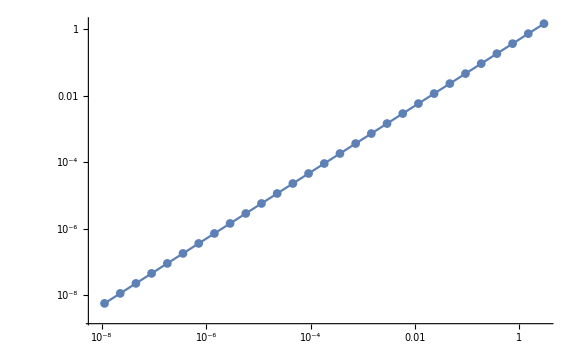

```mathematica
ListLogLogPlot[data,Joined->True,PlotMarkers->Automatic,ImageSize->Large]
```

```mathematica
Last@CoefficientList[Normal[LinearModelFit[Map[Log,data,{2}],{1,x},x]],x]
```

1.

## Secant Method

```mathematica
Example: f(x) = (5-x)*Exp[x]-5
```

```mathematica
fun=(5-x)Exp[x]-5
```

-5+ⅇ^x (5-x)

```mathematica
{res,{evx}}=Reap[FindRoot[fun==0,{x,2,3},Method->"Secant",EvaluationMonitor:>Sow[x]]]
```

{{x→4.56418×10^-14},{{2.,3.,2.,1.04648,1.04648,0.499484,0.499484,0.155456,0.155456,0.0263464,0.0263464,0.00149367,0.00149366,0.0000146946,0.0000146943,8.22889×10^-9,8.22348×10^-9,4.56418×10^-14}}}

```mathematica
ek=Abs[(x/.res)-evx][[2;;;;2]]
```

{3.,1.04648,0.499484,0.155456,0.0263464,0.00149367,0.0000146946,8.22884×10^-9,0.}

```mathematica
data=Transpose[{Most[ek],Rest[ek]}]
```

{{3.,1.04648},{1.04648,0.499484},{0.499484,0.155456},{0.155456,0.0263464},{0.0263464,0.00149367},{0.00149367,0.0000146946},{0.0000146946,8.22884×10^-9},{8.22884×10^-9,0.}}

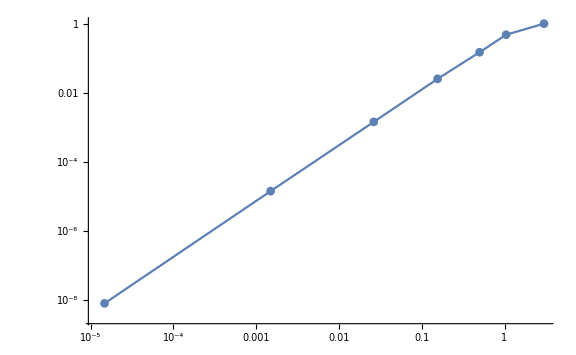

```mathematica
ListLogLogPlot[data,Joined->True,PlotMarkers->Automatic,ImageSize->Large]
```

```mathematica
Last@CoefficientList[Normal[LinearModelFit[Map[Log,Most@data,{2}],{1,x},x]],x]
```

1.56617

## Secant Method

```mathematica
Example: f(x) = x^2
```

```mathematica
fun=x^2
```

x^2

```mathematica
{res,{evx}}=Reap[FindRoot[fun==0,{x,2,3},Method->"Secant",EvaluationMonitor:>Sow[x]]]
```

{{x→1.3841×10^-8},{{2.,3.,2.,1.2,1.2,0.75,0.75,0.461538,0.461538,0.285714,0.285714,0.176471,0.176471,0.109091,0.109091,0.0674157,0.0674157,0.0416667,0.0416667,0.0257511,0.0257511,0.0159151,0.0159151,0.00983607,0.00983606,0.00607903,0.00607902,0.00375704,0.00375704,0.00232198,0.00232198,0.00143506,0.00143506,0.000886918,0.000886917,0.000548145,0.000548145,0.000338773,0.000338772,0.000209373,0.000209372,0.0001294,0.000129399,0.0000799733,0.000079973,0.0000494262,0.000049426,0.0000305471,0.0000305469,0.0000188791,0.000018879,0.000011668,0.0000116678,7.21119×10^-6,7.21109×10^-6,4.45676×10^-6,4.45668×10^-6,2.75443×10^-6,2.75437×10^-6,1.70233×10^-6,1.70228×10^-6,1.0521×10^-6,1.05206×10^-6,6.50233×10^-7,6.50203×10^-7,4.01866×10^-7,4.01843×10^-7,2.48367×10^-7,2.48348×10^-7,1.53499×10^-7,1.53485×10^-7,9.48677×10^-8,9.48563×10^-8,5.86315×10^-8,5.86225×10^-8,3.62362×10^-8,3.62292×10^-8,2.23952×10^-8,2.23897×10^-8,1.3841×10^-8}}}

```mathematica
ek=Abs[evx][[2;;;;2]]
```

{3.,1.2,0.75,0.461538,0.285714,0.176471,0.109091,0.0674157,0.0416667,0.0257511,0.0159151,0.00983607,0.00607903,0.00375704,0.00232198,0.00143506,0.000886918,0.000548145,0.000338773,0.000209373,0.0001294,0.0000799733,0.0000494262,0.0000305471,0.0000188791,0.000011668,7.21119×10^-6,4.45676×10^-6,2.75443×10^-6,1.70233×10^-6,1.0521×10^-6,6.50233×10^-7,4.01866×10^-7,2.48367×10^-7,1.53499×10^-7,9.48677×10^-8,5.86315×10^-8,3.62362×10^-8,2.23952×10^-8,1.3841×10^-8}

```mathematica
data=Transpose[{Most[ek],Rest[ek]}]
```

{{3.,1.2},{1.2,0.75},{0.75,0.461538},{0.461538,0.285714},{0.285714,0.176471},{0.176471,0.109091},{0.109091,0.0674157},{0.0674157,0.0416667},{0.0416667,0.0257511},{0.0257511,0.0159151},{0.0159151,0.00983607},{0.00983607,0.00607903},{0.00607903,0.00375704},{0.00375704,0.00232198},{0.00232198,0.00143506},{0.00143506,0.000886918},{0.000886918,0.000548145},{0.000548145,0.000338773},{0.000338773,0.000209373},{0.000209373,0.0001294},{0.0001294,0.0000799733},{0.0000799733,0.0000494262},{0.0000494262,0.0000305471},{0.0000305471,0.0000188791},{0.0000188791,0.000011668},{0.000011668,7.21119×10^-6},{7.21119×10^-6,4.45676×10^-6},{4.45676×10^-6,2.75443×10^-6},{2.75443×10^-6,1.70233×10^-6},{1.70233×10^-6,1.0521×10^-6},{1.0521×10^-6,6.50233×10^-7},{6.50233×10^-7,4.01866×10^-7},{4.01866×10^-7,2.48367×10^-7},{2.48367×10^-7,1.53499×10^-7},{1.53499×10^-7,9.48677×10^-8},{9.48677×10^-8,5.86315×10^-8},{5.86315×10^-8,3.62362×10^-8},{3.62362×10^-8,2.23952×10^-8},{2.23952×10^-8,1.3841×10^-8}}

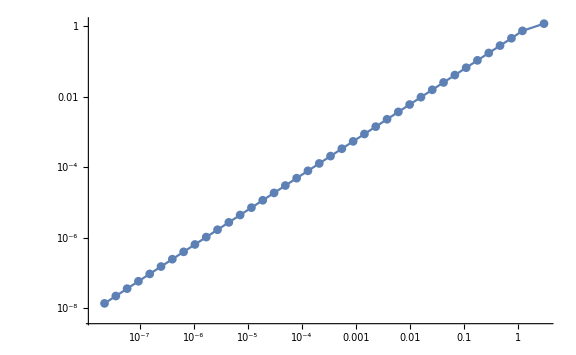

```mathematica
ListLogLogPlot[data,Joined->True,PlotMarkers->Automatic,ImageSize->Large]
```

```mathematica
Last@CoefficientList[Normal[LinearModelFit[Map[Log,data,{2}],{1,x},x]],x]
```

0.996451